# On the Law of Mass-Action for Modeling:

```mathematica
k1=0.4;
k2=0.2;
k3=0.1;
k4=0.25;
k5=0.02;
k6=0.5;
```

```mathematica
odeSystem={
x'[t]==k1-k2 x[t]-k3 x[t] z[t],
x[0]==1,
y'[t]==k3 x[t]z[t]-k5 z[t],
y[0]==1,
z'[t]==-k3 x[t] z[t]+k4 y[t] -k6 z[t],
z[0]==1
};
```

```mathematica
odeSystemTimeEvolution=NDSolve[
odeSystem,
{x,y,z}, (* put your dynamical variables here!*)
{t,0,50} (* total timesteps here! *)
];
```

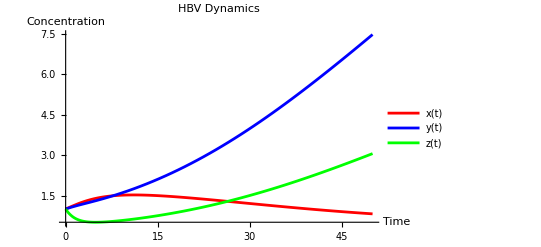

```mathematica
Plot[
Evaluate[{x[t],y[t],z[t]}/. odeSystemTimeEvolution],{t,0,50},
PlotStyle->{Red,Blue,Green},
PlotLegends->{"x(t)","y(t)","z(t)"},
AxesLabel->{"Time","Concentration"},
PlotLabel->"HBV Dynamics"
]
```